```mathematica
o1={-1,0,0};
o2={0,1,0};
v1={3,0,0};
v2={0,-2,0};
```

```mathematica
o1=10{Random[], Random[], Random[]}-5;
o2=10{Random[], Random[], Random[]}-5;
v1=10{Random[], Random[], Random[]}-5;
v2=10{Random[], Random[], Random[]}-5;
a1=10{Random[], Random[], Random[]}-5;
a2=10{Random[], Random[], Random[]}-5;
```

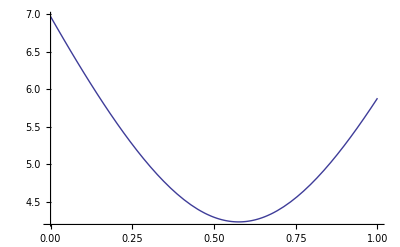

{t→0.575586}

{0.575586}

```mathematica
Plot[Norm[(o1+t v1)-(o2+t v2)],{t,0,1}]
min=Minimize[Norm[(o1+t v1)-(o2+t v2)],{t}][[2]]
{((v2-v1).(o1-o2))/((v2-v1).(v2-v1))}
```

```mathematica
Plot3D[Norm[(o1+t v1)-(o2+v v2)],{t,0,1},{v,0,1}]
min=Minimize[Norm[(o1+t v1)-(o2+v v2)],{t,v}][[2]]
{((o1.v1-o2.v1) (v2.v2)-(o1.v2-o2.v2)(v1.v2))/((v1.v2)^2-(v1.v1) (v2.v2)),((o1-o2).(c{-x z,-y z,x^2+y^2}+b{-x y,x^2+z^2,-y z}+a{y^2+z^2,-x y,-x z}))/((v2×v1).(v2×v1))}/.{a->v2[[1]],b->v2[[2]],c->v2[[3]],x->v1[[1]],y->v1[[2]],z->v1[[3]]}
```

-Graphics3D-

{t→0.0329169,v→-1.4078}

{0.0329171,-1.4078}

```mathematica
ParametricPlot3D[{o1+t v1+t^2 a1,o1+t v1},{t,0,1}]
```

-Graphics3D-

```mathematica
Clear[o1,v1,o2,v2];
o1={o1x,o1y,o1z};
o2={o2x,o2y,o2z};
v1={v1x,v1y,v1z};
v2={v2x,v2y,v2z};
a1={a1x,a1y,a1z};
a2={a2x,a2y,a2z};
```

```mathematica
Solve[{D[Dot[(o1+t v1)-(o2+v v2),(o1+t v1)-(o2+v v2)],t]==0,D[Dot[(o1+t v1)-(o2+v v2),(o1+t v1)-(o2+v v2)]==0,v]},{t,v}]//FullSimplify
```

{{t→-(4 (o1x v2x-o2x v2x+o1y v2y-o2y v2y+o1z v2z-o2z v2z) (v1x v2x+v1y v2y+v1z v2z)-4 (o1x v1x-o2x v1x+o1y v1y-o2y v1y+o1z v1z-o2z v1z) (v2x^2+v2y^2+v2z^2))/(4 (v1x v2x+v1y v2y+v1z v2z)^2-4 (v1x^2+v1y^2+v1z^2) (v2x^2+v2y^2+v2z^2)),v→(o1x v1y^2 v2x-o2x v1y^2 v2x-o1z v1x v1z v2x+o2z v1x v1z v2x+o1x v1z^2 v2x-o2x v1z^2 v2x-o1x v1x v1y v2y+o2x v1x v1y v2y-o1z v1y v1z v2y+o2z v1y v1z v2y+((o1z-o2z) (v1x^2+v1y^2)+(-o1x+o2x) v1x v1z) v2z+o2y (v1x v1y v2x-v1x^2 v2y-v1z^2 v2y+v1y v1z v2z)+o1y (-v1x v1y v2x+v1x^2 v2y+v1z (v1z v2y-v1y v2z)))/(v1z^2 (v2x^2+v2y^2)-2 v1x v1z v2x v2z-2 v1y v2y (v1x v2x+v1z v2z)+v1y^2 (v2x^2+v2z^2)+v1x^2 (v2y^2+v2z^2))}}

```mathematica
sols=Solve[{D[Dot[(o1+t v1+t^2 a1)-(o2+v v2+v^2 a2),(o1+t v1+t^2 a1)-(o2+v v2+v^2 a2)],t]==0,D[Dot[(o1+t v1)-(o2+v v2),(o1+t v1)-(o2+v v2)]==0,v]},{t,v}];
```